## 1. Initialisation

Set publication-quality defaults for ComplexListPlot (font, axes colour).
All subsequent ComplexListPlot calls inherit these options.

```mathematica
(*Set default ComplexListPlot options: Latin Modern Roman font at 14 pt,
  black axes with black tick labels — publication style.*)
SetOptions[ComplexListPlot,
  BaseStyle  -> {FontFamily -> "Latin Modern Roman", FontSize -> 14},
  AxesStyle  -> Directive[Black, FontColor -> Black]
];
```

## 2. Non-Hermitian Bloch Hamiltonian

Define the d-vector and Pauli-matrix basis (arXiv:2606.24705, Eq.(2),
https://arxiv.org/abs/2606.24705).
H_RM(kappa) = d . sigma, where
  d = {epsilon_p - 2m cos(kappa), -t - t' cos(kappa), -t' sin(kappa), epsilon_m + i*gamma}
  sigma = {I_2, sigma_1, sigma_2, sigma_3}
The complex conjugation helper CC[ ] is used when checking EP conditions.

```mathematica
(*Complex conjugation: replace every Complex[a,b] by Complex[a,-b].*)
CC[arg_] := arg /. Complex[a_, b_] :> Complex[a, -b];

(*d-vector components (arXiv:2606.24705, Eq.(2)): d = {d0, d1, d2, d3}.
  d0 = epsilon_p - 2m*cos(kappa)  [NNN identity term]
  d1 = -t - t'*cos(kappa)         [real off-diagonal]
  d2 = -t'*sin(kappa)             [imaginary off-diagonal]
  d3 = epsilon_m + I*gamma        [non-Hermitian on-site imbalance] *)
d = {ϵp - 2 m Cos[κ],
     -t - tp Cos[κ],
     -tp Sin[κ],
     ϵm + I γ};

(*Pauli matrix basis: sigma = {I_2, sigma_x, sigma_y, sigma_z}.*)
σ = {IdentityMatrix[2],
            {{0, 1}, {1, 0}},
            {{0, -I}, {I, 0}},
            {{1, 0}, {0, -1}}};
```

## 3. Exceptional-point conditions

EPs occur where two eigenvalues AND two eigenvectors coalesce.
For H = d.sigma, two simultaneous conditions must hold (arXiv:2606.24705, Sec. II, Eqs.(5a)-(5b),
https://arxiv.org/abs/2606.24705):
  (i)  Re[d].Re[d] - Im[d].Im[d] = 0
  (ii) Re[d].Im[d] = 0
For epsilon_m = 0 condition (ii) reduces to gamma*epsilon_m = 0, which is
automatic; the EP threshold is then gamma_c(kappa) = Sqrt[t^2+t'^2+2tt'cos(kappa)]
(arXiv:2606.24705, Eq.(6)).

```mathematica
(*EP condition (i): Re[d].Re[d] - Im[d].Im[d] must vanish (arXiv:2606.24705, Eq.(5a)).*)
epCondI = FullSimplify[
  ComplexExpand[Re[d] . Re[d] - Im[d] . Im[d]]
];

(*EP condition (ii): Re[d].Im[d] must vanish.
  With epsilon_m -> 0 this becomes gamma*epsilon_m = 0, trivially satisfied.*)
epCondII = FullSimplify[Re[d] . Im[d],
  Assumptions -> {ϵm ∈ Reals,
                   γ   ∈ Reals}
];

(*Bulk dispersion E_pm(kappa) from Eigensystem of d.sigma (arXiv:2606.24705, Eq.(4)):
  E_pm = epsilon_p - 2m*cos(kappa) +/- Sqrt[t^2+t'^2+2tt'cos(kappa)-(gamma-i*epsilon_m)^2] *)
{en, vec} = Eigensystem[d . σ] // FullSimplify;

(*Special case epsilon_m = 0: dispersion becomes real-valued under the EP threshold.*)
enA = en /. ϵm -> 0;
```

## 4. EP marker and helper functions

EPmarker draws a coloured point with a black circle outline at the EP
position in the complex-energy plane. The circle radius is given in scaled
(plot-fraction) coordinates so it stays the same size regardless of PlotRange.
cosKEP, EPreal, EPexists compute the EP momentum, the corresponding real-energy
position on the Im[E]=0 axis, and whether the EP exists (|cos(kappa_EP)| <= 1).

```mathematica
(*EPmarker: coloured Point at pos with a black Circle of radius 0.015
  in scaled coordinates, and AbsoluteThickness 1.2 for the circle stroke.
  The star version (Inset[Style[FivePointedStar,...]]) is commented out below;
  switch the active definition to use stars instead of circles.*)
EPmarker[pos_, color_] := {color, PointSize[0.025], Point[pos], Black,
   AbsoluteThickness[1.2], Circle[pos, Scaled[{0.015, 0.015}]]};

(*Alternative star marker (centred on pos via {Center,Center}):*)
(*EPmarker[pos_, color_] := Inset[
     Style["★", color, FontSize -> 18, FontWeight -> Bold],
     pos, {Center, Center}];*)

(*Fix tp = 1 throughout; epsPlus is the reference on-site energy.*)
epsPlus = 1;

(*cosKEP: cos(kappa_EP) from the EP threshold condition (arXiv:2606.24705, Eq.(6))
  gamma_c^2 = t^2+tp^2+2tt'cos(kappa).
  Solved for cos(kappa) with tp = 1.*)
cosKEP[t_, gamma_] := (gamma^2 - t^2 - tp^2)/(2 t tp) /. tp -> 1;

(*EPreal: Re[E] at the EP, equals epsPlus - 2m*cos(kappa_EP) (Im[E]=0 at EP).*)
EPreal[m_, t_, gamma_] := (epsPlus - 2 m cosKEP[t, gamma]) /. tp -> 1;

(*EPexists: True when |cos(kappa_EP)| <= 1, i.e. the EP lies in the Brillouin zone.*)
EPexists[t_, gamma_] := (Abs[cosKEP[t, gamma]] <= 1) /. tp -> 1;
```

## 5. Panel A — complex spectrum, t=1/2, gamma=1.4

Panel (a) of Fig. 2: ComplexListPlot of E_pm(kappa) in the complex plane
for t=1/2 < t'=1 (|t-t'|=0.5 < gamma_c < t+t'=1.5) and gamma=1.4.
Three values of the staggered hopping m are shown: m=0, m=t', m=2t'.
Green circle markers indicate EP positions computed by EPmarker.

```mathematica
(*Parameters for panel (a): t=1/2, tp=1, gamma=1.4, epsilon_p=1, nn=500 kappa points.*)
var = {t -> 1/2, tp -> 1, γ -> 14/10, ϵp -> 1, nn -> 500};

(*Sample E_pm(kappa) over the Brillouin zone for m = 0, 1, 2 (in units of tp=1).
  E_+ and E_- give six coloured series for the ComplexListPlot.*)
enRPBCBlochPm0PanA = Table[(ϵp - 2 m Cos[κ] -
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 0,
  {κ, -π, π, 2π/(nn /. var)}];
enRPBCBlochNm0PanA = Table[(ϵp - 2 m Cos[κ] +
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 0,
  {κ, -π, π, 2π/(nn /. var)}];
enRPBCBlochPm1PanA = Table[(ϵp - 2 m Cos[κ] -
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 1,
  {κ, -π, π, 2π/(nn /. var)}];
enRPBCBlochNm1PanA = Table[(ϵp - 2 m Cos[κ] +
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 1,
  {κ, -π, π, 2π/(nn /. var)}];
enRPBCBlochPm2PanA = Table[(ϵp - 2 m Cos[κ] -
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 2,
  {κ, -π, π, 2π/(nn /. var)}];
enRPBCBlochNm2PanA = Table[(ϵp - 2 m Cos[κ] +
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 2,
  {κ, -π, π, 2π/(nn /. var)}];

(*Compute EP positions in the complex plane; EPmarker returns {} when EP does not exist.*)
panelAmarkers = With[{tv = t /. var, gv = γ /. var},
  Graphics[{
    If[EPexists[tv, gv], EPmarker[{EPreal[0, tv, gv], 0}, Green], {}],
    If[EPexists[tv, gv], EPmarker[{EPreal[1, tv, gv], 0}, Green], {}],
    If[EPexists[tv, gv], EPmarker[{EPreal[2, tv, gv], 0}, Green], {}]
  }]];

(*Fig. 2(a): ComplexListPlot of the six energy series; overlay EP markers and panel label.*)
panelA = Show[
  ComplexListPlot[
    {enRPBCBlochPm0PanA, enRPBCBlochNm0PanA,
     enRPBCBlochPm1PanA, enRPBCBlochNm1PanA,
     enRPBCBlochPm2PanA, enRPBCBlochNm2PanA},
    Frame -> False, AspectRatio -> 1,
    PlotStyle -> {{Red,    PointSize[0.0125]}, {Red,    PointSize[0.0125]},
                  {Blue,   PointSize[0.0125]}, {Blue,   PointSize[0.0125]},
                  {Orange, PointSize[0.0125]}, {Orange, PointSize[0.0125]}},
    PlotLegends -> Placed[
      {"m=0", None, "m=t'", None, "m=2t'", None},
      {0.1, 0.15}],
    AxesLabel -> {"Re[ℰ]/t'", "Im[ℰ]/t'"},
    AspectRatio -> Automatic, PlotRange -> {Automatic},
    Background -> None],
  panelAmarkers,
  Graphics@Text[Style["(a)", Large], {-3, 1.3}]
];
```

## 6. Panel B — complex spectrum, t=1/2, gamma=1.6

Panel (b) of Fig. 2: same hopping t=1/2 as (a) but gamma=1.6 > t+t'=1.5.
Above the upper EP threshold: all eigenvalues have non-zero imaginary part.

```mathematica
(*Parameters for panel (b): gamma raised to 1.6 — above the EP threshold gamma_c(0)=t+t'.*)
var = {t -> 1/2, tp -> 1, γ -> 16/10, ϵp -> 1, nn -> 500};

(*Sample E_pm for m = 0, 1, 2 as in panel (a).*)
enRPBCBlochPm0PanB = Table[(ϵp - 2 m Cos[κ] -
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 0,
  {κ, -π, π, 2π/(nn /. var)}];
enRPBCBlochNm0PanB = Table[(ϵp - 2 m Cos[κ] +
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 0,
  {κ, -π, π, 2π/(nn /. var)}];
enRPBCBlochPm1PanB = Table[(ϵp - 2 m Cos[κ] -
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 1,
  {κ, -π, π, 2π/(nn /. var)}];
enRPBCBlochNm1PanB = Table[(ϵp - 2 m Cos[κ] +
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 1,
  {κ, -π, π, 2π/(nn /. var)}];
enRPBCBlochPm2PanB = Table[(ϵp - 2 m Cos[κ] -
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 2,
  {κ, -π, π, 2π/(nn /. var)}];
enRPBCBlochNm2PanB = Table[(ϵp - 2 m Cos[κ] +
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 2,
  {κ, -π, π, 2π/(nn /. var)}];

panelAmarkers = With[{tv = t /. var, gv = γ /. var},
  Graphics[{
    If[EPexists[tv, gv], EPmarker[{EPreal[0, tv, gv], 0}, Green], {}],
    If[EPexists[tv, gv], EPmarker[{EPreal[1, tv, gv], 0}, Green], {}],
    If[EPexists[tv, gv], EPmarker[{EPreal[2, tv, gv], 0}, Green], {}]
  }]];

(*Fig. 2(b): no EP markers shown because gamma > t+t' places no real-kappa EP in BZ.*)
panelB = Show[
  ComplexListPlot[
    {enRPBCBlochPm0PanB, enRPBCBlochNm0PanB,
     enRPBCBlochPm1PanB, enRPBCBlochNm1PanB,
     enRPBCBlochPm2PanB, enRPBCBlochNm2PanB},
    Frame -> False, AspectRatio -> 1,
    PlotStyle -> {{Red,    PointSize[0.0125]}, {Red,    PointSize[0.0125]},
                  {Blue,   PointSize[0.0125]}, {Blue,   PointSize[0.0125]},
                  {Orange, PointSize[0.0125]}, {Orange, PointSize[0.0125]}},
    PlotLegends -> Placed[
      {"m=0", None, "m=t'", None, "m=2t'", None},
      {0.1, 0.15}],
    AxesLabel -> {"Re[ℰ]/t'", "Im[ℰ]/t'"},
    AspectRatio -> Automatic, PlotRange -> {Automatic},
    Background -> None],
  panelAmarkers,
  Graphics@Text[Style["(b)", Large], {-3, 1.3}]
];
```

## 7. Panel C — complex spectrum, t=3/2, gamma=1.4

Panel (c) of Fig. 2: t=3/2 > t'=1. Now t > t' so the lower EP threshold
is gamma_c(pi) = |t - t'| = 0.5 and the upper is gamma_c(0) = t+t' = 2.5.
At gamma=1.4 the system is between the two thresholds.

```mathematica
(*Parameters for panel (c): t raised to 3/2, same gamma = 1.4.*)
var = {t -> 3/2, tp -> 1, γ -> 14/10, ϵp -> 1, nn -> 500};

enRPBCBlochPm0PanC = Table[(ϵp - 2 m Cos[κ] -
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 0,
  {κ, -π, π, 2π/(nn /. var)}];
enRPBCBlochNm0PanC = Table[(ϵp - 2 m Cos[κ] +
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 0,
  {κ, -π, π, 2π/(nn /. var)}];
enRPBCBlochPm1PanC = Table[(ϵp - 2 m Cos[κ] -
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 1,
  {κ, -π, π, 2π/(nn /. var)}];
enRPBCBlochNm1PanC = Table[(ϵp - 2 m Cos[κ] +
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 1,
  {κ, -π, π, 2π/(nn /. var)}];
enRPBCBlochPm2PanC = Table[(ϵp - 2 m Cos[κ] -
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 2,
  {κ, -π, π, 2π/(nn /. var)}];
enRPBCBlochNm2PanC = Table[(ϵp - 2 m Cos[κ] +
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 2,
  {κ, -π, π, 2π/(nn /. var)}];

panelAmarkers = With[{tv = t /. var, gv = γ /. var},
  Graphics[{
    If[EPexists[tv, gv], EPmarker[{EPreal[0, tv, gv], 0}, Green], {}],
    If[EPexists[tv, gv], EPmarker[{EPreal[1, tv, gv], 0}, Green], {}],
    If[EPexists[tv, gv], EPmarker[{EPreal[2, tv, gv], 0}, Green], {}]
  }]];

(*Fig. 2(c): t=3/2 places EP markers at different Re[E] positions than panel (a).*)
panelC = Show[
  ComplexListPlot[
    {enRPBCBlochPm0PanC, enRPBCBlochNm0PanC,
     enRPBCBlochPm1PanC, enRPBCBlochNm1PanC,
     enRPBCBlochPm2PanC, enRPBCBlochNm2PanC},
    Frame -> False, AspectRatio -> 1,
    PlotStyle -> {{Red,    PointSize[0.0125]}, {Red,    PointSize[0.0125]},
                  {Blue,   PointSize[0.0125]}, {Blue,   PointSize[0.0125]},
                  {Orange, PointSize[0.0125]}, {Orange, PointSize[0.0125]}},
    PlotLegends -> Placed[
      {"m=0", None, "m=t'", None, "m=2t'", None},
      {0.1, 0.15}],
    AxesLabel -> {"Re[ℰ]/t'", "Im[ℰ]/t'"},
    AspectRatio -> Automatic, PlotRange -> {Automatic},
    Background -> None],
  panelAmarkers,
  Graphics@Text[Style["(c)", Large], {-3, 1.3}]
];
```

## 8. Panel D — complex spectrum, t=3/2, gamma=1.6

Panel (d) of Fig. 2: t=3/2, gamma=1.6 — still within the EP window
[|t-t'|, t+t'] = [0.5, 2.5]. Compare with panel (b): different EP positions
due to the larger NN hopping t.

```mathematica
(*Parameters for panel (d): t=3/2, gamma=1.6.*)
var = {t -> 3/2, tp -> 1, γ -> 16/10, ϵp -> 1, nn -> 500};

enRPBCBlochPm0PanD = Table[(ϵp - 2 m Cos[κ] -
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 0,
  {κ, -π, π, 2π/(nn /. var)}];
enRPBCBlochNm0PanD = Table[(ϵp - 2 m Cos[κ] +
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 0,
  {κ, -π, π, 2π/(nn /. var)}];
enRPBCBlochPm1PanD = Table[(ϵp - 2 m Cos[κ] -
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 1,
  {κ, -π, π, 2π/(nn /. var)}];
enRPBCBlochNm1PanD = Table[(ϵp - 2 m Cos[κ] +
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 1,
  {κ, -π, π, 2π/(nn /. var)}];
enRPBCBlochPm2PanD = Table[(ϵp - 2 m Cos[κ] -
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 2,
  {κ, -π, π, 2π/(nn /. var)}];
enRPBCBlochNm2PanD = Table[(ϵp - 2 m Cos[κ] +
    Sqrt[t^2 + tp^2 - γ^2 + 2 t tp Cos[κ]]) /. var /. m -> 2,
  {κ, -π, π, 2π/(nn /. var)}];

panelAmarkers = With[{tv = t /. var, gv = γ /. var},
  Graphics[{
    If[EPexists[tv, gv], EPmarker[{EPreal[0, tv, gv], 0}, Green], {}],
    If[EPexists[tv, gv], EPmarker[{EPreal[1, tv, gv], 0}, Green], {}],
    If[EPexists[tv, gv], EPmarker[{EPreal[2, tv, gv], 0}, Green], {}]
  }]];

(*Fig. 2(d): ComplexListPlot with EP markers for t=3/2, gamma=1.6.*)
panelD = Show[
  ComplexListPlot[
    {enRPBCBlochPm0PanD, enRPBCBlochNm0PanD,
     enRPBCBlochPm1PanD, enRPBCBlochNm1PanD,
     enRPBCBlochPm2PanD, enRPBCBlochNm2PanD},
    Frame -> False, AspectRatio -> 1,
    PlotStyle -> {{Red,    PointSize[0.0125]}, {Red,    PointSize[0.0125]},
                  {Blue,   PointSize[0.0125]}, {Blue,   PointSize[0.0125]},
                  {Orange, PointSize[0.0125]}, {Orange, PointSize[0.0125]}},
    PlotLegends -> Placed[
      {"m=0", None, "m=t'", None, "m=2t'", None},
      {0.1, 0.15}],
    AxesLabel -> {"Re[ℰ]/t'", "Im[ℰ]/t'"},
    AspectRatio -> Automatic, PlotRange -> {Automatic},
    Background -> None],
  panelAmarkers,
  Graphics@Text[Style["(d)", Large], {-3, 1.3}]
];
```

## 9. Final figure — GraphicsGrid of all four panels

Assemble the four panels into a 2x2 grid: top row (a,b) has t=1/2;
bottom row (c,d) has t=3/2. Left column (a,c) has gamma=1.4; right column (b,d) has gamma=1.6.
ImageSize->Full stretches the grid to fill the notebook window.

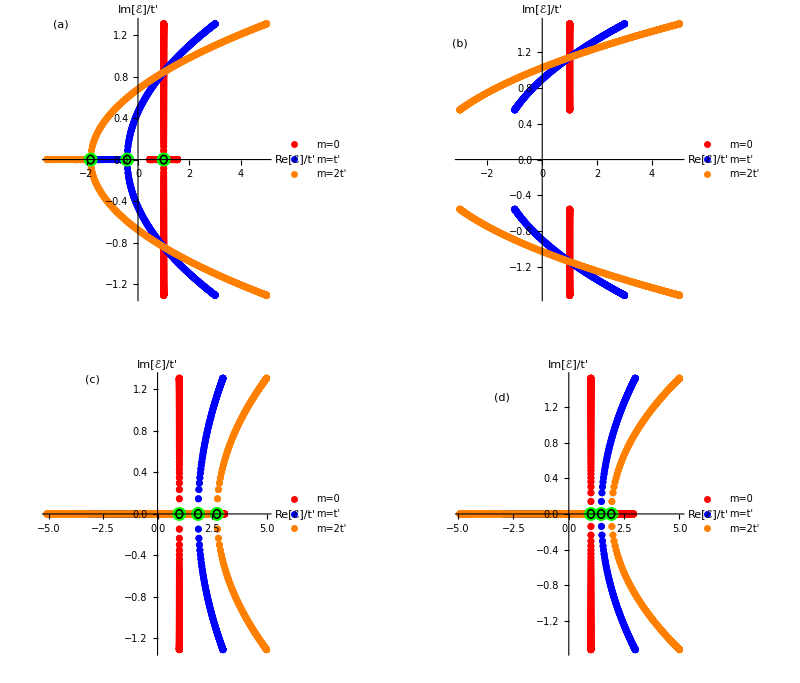

```mathematica
(*Fig. 2: assemble panels in a 2x2 GraphicsGrid.
  Row 1: panels A (t=1/2, gamma=1.4) and B (t=1/2, gamma=1.6)
  Row 2: panels C (t=3/2, gamma=1.4) and D (t=3/2, gamma=1.6) *)
GraphicsGrid[
  {{panelA, panelB},
   {panelC, panelD}},
  ImageSize -> Full
]
```